```mathematica
(*Blade Arnold TTH at 2:00*)
(*1 (10 points).Use the function StreamPlot to reproduce the given computer-generated direction field between
[−5,5] including letting Mathematica sketch the approximate solution curve(in red)that passes through the
point 𝑦(𝜋 4)=𝜋8.*)
```

```mathematica
p1 =StreamPlot[{1, Sinh[x] Cosh[y]}, {x,-5,5}, {y,-5,5}];
DSolve[{y'[x]==Sinh[x]Cosh[y[x]], y[π/4]==π/8},y[x],x]
```

{{y[x]→2 ArcTanh[Tan[1/4 (2 (2 ArcTan[Tanh[π/16]]-Cosh[π/4])+2 Cosh[x])]]}}

```mathematica
p2 = Plot[2 ArcTanh[Tan[1/4 (2 (2 ArcTan[Tanh[π/16]]-Cosh[π/4])+2 Cosh[x])]], {x,-5,5},PlotStyle->Red];
```

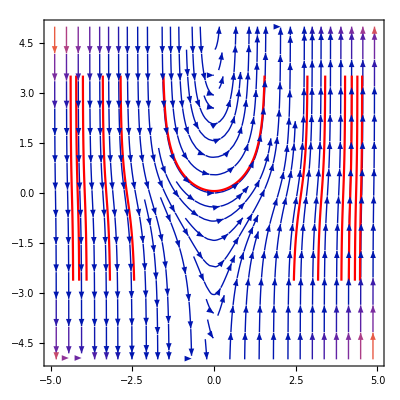

```mathematica
Show[p1,p2]
```

```mathematica
(*2. (10 points).Solve the following differential equation.Use//Expand after the command to reduce.*)
Clear

DSolve[{x^3  y'''[x]+3x^2y''[x]+6x y'[x]+y[x]==ln(x)-47/8},y[x],x]//Expand
```

Clear

{{y[x]→x^(Root-0.198Root[1+5 #1+#1^3&,1]-0.19843721453862295) C[1]+x^(Root0.0992-2.24 ⅈRoot[1+5 #1+#1^3&,2]0.09921860726931148) C[2]+202+(ln x Root0.0992-2.24 ⅈRoot[1+5 #1+#1^3&,2]0.09921860726931148 (Root0.0992+2.24 ⅈRoot[1+5 #1+#1^3&,3]0.09921860726931148)^5)/((Root-0.198Root[1+5 #1+#1^3&,1]-0.19843721453862295-Root0.0992-2.24 ⅈRoot[1+5 #1+#1^3&,2]0.09921860726931148) (-1+Root0.0992-2.24 ⅈRoot[1+5 #1+#1^3&,2]0.09921860726931148) 5 (-5+(Root0.0992-2.24 ⅈRoot[1+5 #1+#1^3&,2]0.09921860726931148)^2+2 Root-0.198Root[1+5 #1+#1^3&,1]-0.19843721453862295 Root0.0992+2.24 ⅈRoot[1+5 #1+#1^3&,3]0.09921860726931148))}}
 |  |  |  |

```mathematica
(*3. Solve the following differential equation.Use//Simplify after the command to reduce.*)
```

```mathematica
DSolve[{y''[x]-4y''[x]+8y[x]==(2x^2-3x)e^2x Cos(2x)+(10x^2-x-1)e^2x Sin(2x),y[0]==π/2, y[3]==π},y[x],x]//Simplify
```

{{y[x]→1/(16 (-1+ⅇ^(4 √6)))ⅇ^(-2 √(2/3) x) (ⅇ^(2 √(2/3) (3+2 x)) (16 π-4821 e^2 Sin)+4 ⅇ^(4 √6) (2 π-33 e^2 Sin)+ⅇ^(4 √(2/3) x) (-8 π+132 e^2 Sin)+ⅇ^(2 √6) (-16 π+4821 e^2 Sin)-e^2 ⅇ^(2 √(2/3) x) Sin (132-9 x+176 x^2-4 x^3+40 x^4)+e^2 ⅇ^(2 √(2/3) (6+x)) Sin (132-9 x+176 x^2-4 x^3+40 x^4)-Cos e^2 (-594 ⅇ^(2 √6)+27 ⅇ^(4 √6)-27 ⅇ^(4 √(2/3) x)+594 ⅇ^(2 √(2/3) (3+2 x))+ⅇ^(2 √(2/3) (6+x)) (-27+27 x-36 x^2+12 x^3-8 x^4)+ⅇ^(2 √(2/3) x) (27-27 x+36 x^2-12 x^3+8 x^4)))}}

```mathematica
(*4. (30 points).A competition model defined by*)
S=NDSolve[{x'[t]==x[t](x[t](2-2/5x[t]-3/10y[t])),y'[t]==y[t](y[t](1-1/10y[t]-3/10x[t])),x[0]==4,y[0]==5} ,{x[t],y[t]},{t,0,300}];
```

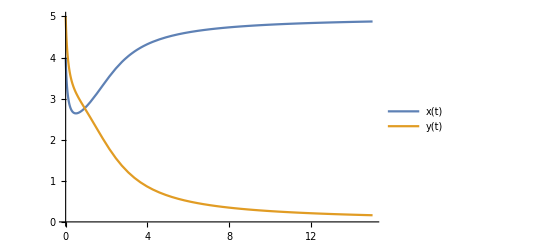

```mathematica
Plot[Evaluate[{x[t],y[t]}/.S],{t,0,15},PlotLegends->{x[t],y[t]}]
```

```mathematica
(*It will take about 1 year for the x[t] population to surpass the other*)

(*5.(10 points).Solve the given differential equation by using Mathematica.*)
```

```mathematica
DSolve[{5.23y'''[x]+4.76y''[x]+8.39y'[x]+0.625y[x]==0},y[x],x]
```

{{y[x]→ⅇ^(-0.0776201 x) C[3]+ⅇ^(-0.416257 x) C[2] Cos[1.1689 x]+ⅇ^(-0.416257 x) C[1] Sin[1.1689 x]}}

```mathematica
(*6. (10 points).Use the reduction of order formula to find the second solution to the following differential
equation.*)
```

```mathematica
y[x_]:=u[x]*3/x^(7/5);
```

```mathematica
y'[x]
```

-(21 u[x])/(5 x^(12/5))+(3 u'[x])/x^(7/5)

```mathematica
y''[x]
```

(252 u[x])/(25 x^(17/5))-(42 u'[x])/(5 x^(12/5))+(3 u''[x])/x^(7/5)

```mathematica
a =Simplify[5x^2 y''[x]+17x y'[x]+7y[x]]
```

(3 (7-7 u[x]+3 x u'[x]+5 x^2 u''[x]))/x^(7/5)

```mathematica
DSolveValue[a==0,u[x],x]
```

1+C[1]/x+x^(7/5) C[2]

```mathematica
(*Second solution will be 3/x + 3*)

(*7.(10 points).Find the Laplace Transform of the following:*)
```

```mathematica
LaplaceTransform[10Exp[7t]+5t Exp[2t]+Cosh[3t], t, s]
```

10/(-7+s)+5/(-2+s)^2+s/(-9+s^2)

```mathematica
LaplaceTransform[Sin[2t]+500t^4 +Exp[t]Cos[5t], t, s]
```

(-1+s)/(25+(-1+s)^2)+12000/s^5+2/(4+s^2)

```mathematica
LaplaceTransform[t^6 e Exp[4t]+t  δ(t-2), t, s]
```

```mathematica
(720 e)/(-4+s)^7+(2 δ)/s^3-(2 δ)/s^2
```

```mathematica
LaplaceTransform[(3t-2)∪(t-4), t, s]
```

4/s^2-6/s

```mathematica
(*8. (10 points).Find the Inverse Laplace Transform of the following:*)
```

```mathematica
InverseLaplaceTransform[s/((s-1)^2(s^2+1)(s^2-1)), s, t]
```

ⅇ^-t/16-ⅇ^t/16-(ⅇ^t t)/8+(ⅇ^t t^2)/8+Sin[t]/4

```mathematica
InverseLaplaceTransform[Exp[-2s]/(s^2+4s+5), s, t]
```

-1/2 ⅈ ⅇ^((-2-ⅈ) (-2+t)) (-1+ⅇ^(2 ⅈ (-2+t))) HeavisideTheta[-2+t]

```mathematica
InverseLaplaceTransform[240s/(s-9)^7 +24s/(s^2+9)^2, s, t]
```

ⅇ^(9 t) t^5 (2+3 t)+4 t Sin[3 t]

```mathematica
InverseLaplaceTransform[1, s, t]
```

DiracDelta[t]